# Analiza smrtnosti otrok zaradi malarije v letih 2000-2015

## Pridobivanje podatkov

Podatke bom vzel iz Wolfram data repository.

```mathematica
podatki = ResourceData["Child Mortality from Malaria"];
```

## Prikaz podatkov nekaterih držav v Afriki, Aziji in Južni Ameriki

Naslednje države sem si izbral, saj so to bile po podatkih dobljenih predvsem na spletnih straneh organizacije WHO države z največjo umrljivostjo po kontinentih. Za državo z največ umrlih iz naštetih kontinentov bom prikazal kako se je spreminjalo število umrlih glede na prejšnje leto .

### Afrika

Te države sem si izbral, saj se tam zgodi skoraj 50% vseh smrtnih primerov zaradi malarije na svetovni ravni.

```mathematica
drzaveAfrika = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAfrikaVrstice=Select[podatki,MemberQ[ drzaveAfrika,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 27 dni ter 0 - 4 let.

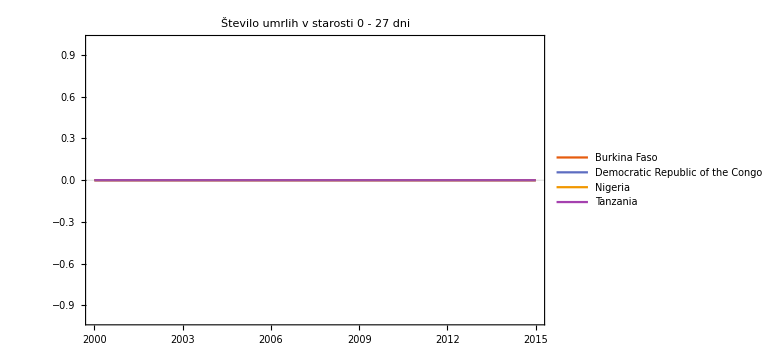

```mathematica
DateListPlot[#["Aged0To27Days"]&/@drzaveAfrikaVrstice,PlotLegends->Table[drzaveAfrikaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 27 dni",PlotTheme->"Scientific",ImageSize->Large]
```

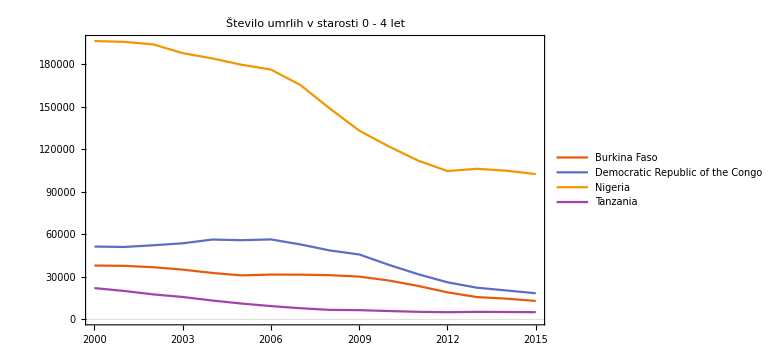

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAfrikaVrstice,PlotLegends->Table[drzaveAfrikaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 4 let",PlotTheme->"Scientific",ImageSize->Large]
```

Prikaz spreminjanja števila umrlih glede na prejšnje leto .

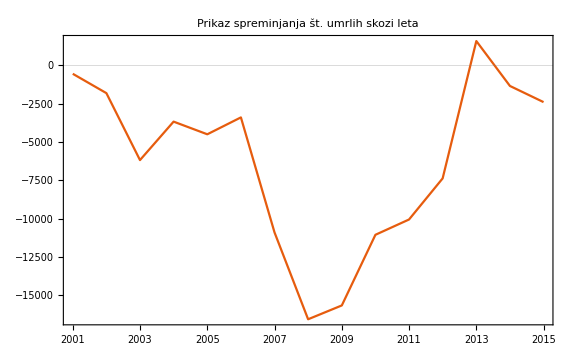

```mathematica
DateListPlot[Differences[ Select[podatki, #["Country"]== LinguisticAssistant&][[1]]["Aged0To4Years"]],PlotTheme->"Scientific",PlotLabel->"Prikaz spreminjanja št. umrlih skozi leta",ImageSize->Large]
```

### Azija

```mathematica
drzaveAzija = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAzijaVrstice=Select[podatki,MemberQ[ drzaveAzija,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 4 let .

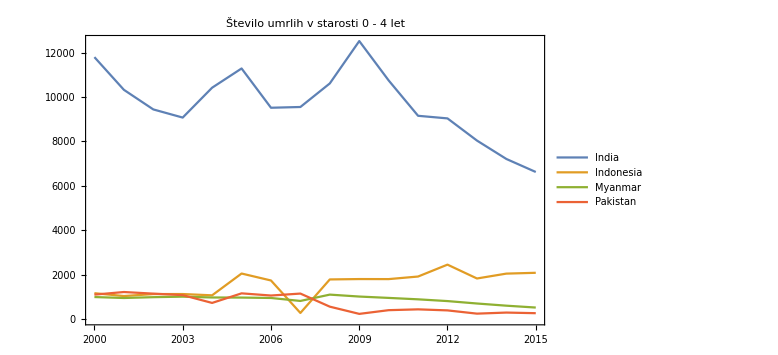

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAzijaVrstice,PlotLegends->Table[drzaveAzijaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 4 let",ImageSize->Large]
```

Prikaz spreminjanja števila umrlih glede na prejšnje leto .

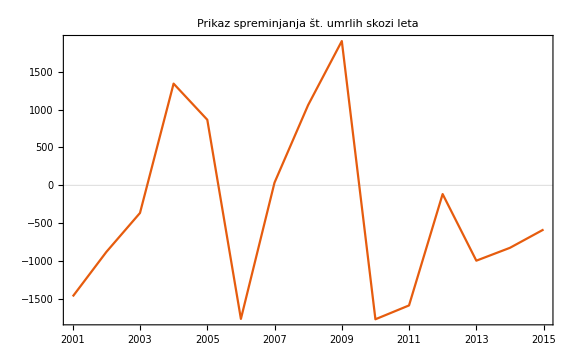

```mathematica
DateListPlot[Differences[ Select[podatki, #["Country"]== LinguisticAssistant&][[1]]["Aged0To4Years"]],PlotTheme->"Scientific",PlotLabel->"Prikaz spreminjanja št. umrlih skozi leta",ImageSize->Large]
```

### Južna Amerika in Karibi

```mathematica
drzaveAmerika = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAmerikaVrstice=Select[podatki,MemberQ[ drzaveAmerika,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 4 let .

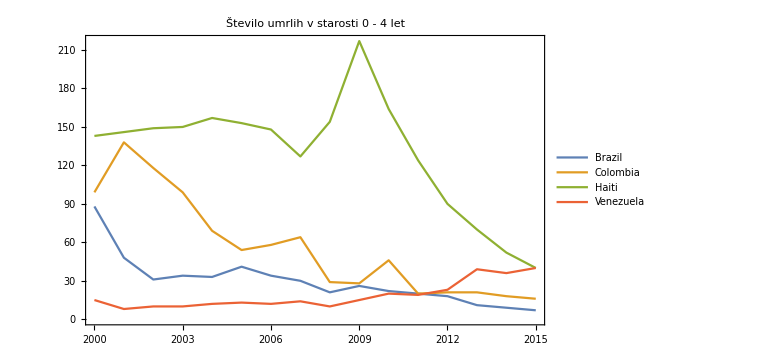

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAmerikaVrstice,PlotLegends->Table[drzaveAmerikaVrstice[[x]]["Country"],{x,1,4}], PlotLabel->"Število umrlih v starosti 0 - 4 let",ImageSize->Large]
```

Prikaz spreminjanja števila umrlih glede na prejšnje leto .

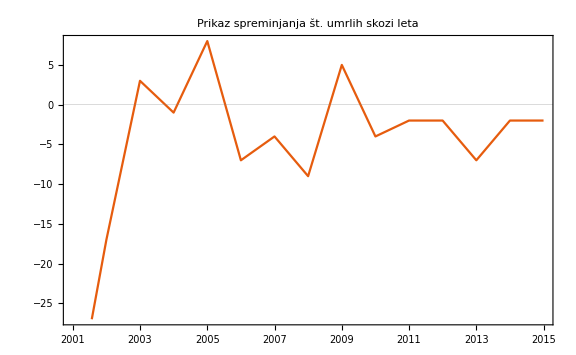

```mathematica
DateListPlot[Differences[ Select[podatki, #["Country"]== LinguisticAssistant&][[1]]["Aged0To4Years"]],PlotTheme->"Scientific",PlotLabel->"Prikaz spreminjanja št. umrlih skozi leta",ImageSize->Large]
```

### Ugotovitev

Po pregledu podatkov sem ugotovil, da ni zabeleženih smrti v razponu 0 - 27 dni zato sem to prikazal le pri Afriki, saj so bili vsi grafi s tem razponom le ravne črte, ki so prekrivale ena drugo tako da se ni dalo iz njih nič razbrati. Po pričakovanjih sem ugotovil da je največ smrtih primerov v Afriki, predvsem v podsaharski in v območju ekvatorja. Zanimivo se mi je tudi zdelo nihanje števila umrlih skozi leta, saj krivulja niha in je težko napovedati trend za prihodnost.

## Prikaz stanja v državah v časovnem obdobju 10 let

### Afrika

```mathematica
VseDrzaveAfrike = EntityList[EntityClass["Country","Africa"]];
```

```mathematica
PodatkiCelotnaAfrika = Select[podatki,MemberQ[VseDrzaveAfrike, #["Country"]]&];
```

#### Prikaz za leto 2005

```mathematica
GeoRegionValuePlot[Table[PodatkiCelotnaAfrika[[x]]["Country"]->100000*PodatkiCelotnaAfrika[[x]]["Aged0To4Years"]["2005"]/PodatkiCelotnaAfrika[[x]]["Country"]["Population"],{x,Length[PodatkiCelotnaAfrika]}],PlotTheme->"Scientific",PlotLabel->"Prikaz umrlih na 100 000 prebivalcev za leto 2005",ImageSize->Large]
```

-Graphics-

#### prikaz za leto 2015

```mathematica
GeoRegionValuePlot[Table[PodatkiCelotnaAfrika[[x]]["Country"]->100000*PodatkiCelotnaAfrika[[x]]["Aged0To4Years"]["2015"]/PodatkiCelotnaAfrika[[x]]["Country"]["Population"],{x,Length[PodatkiCelotnaAfrika]}],PlotTheme->"Scientific",PlotLabel->"Prikaz umrlih na 100 000 prebivalcev za leto 2015",ImageSize->Large]
```

-Graphics-

### Azija

```mathematica
VseDrzaveAzija = EntityList[EntityClass["Country","Asia"]];
```

```mathematica
PodatkiCelotnaAzija = Select[podatki,MemberQ[VseDrzaveAzija, #["Country"]]&];
```

#### Leto 2005

```mathematica
GeoRegionValuePlot[Table[PodatkiCelotnaAzija[[x]]["Country"]->100000*PodatkiCelotnaAzija[[x]]["Aged0To4Years"]["2005"]/PodatkiCelotnaAzija[[x]]["Country"]["Population"],{x,Length[PodatkiCelotnaAzija]}],PlotTheme->"Scientific",PlotLabel->"Prikaz umrlih na 100 000 prebivalcev za leto 2005",ImageSize->Large]
```

-Graphics-

#### Leto 2015

```mathematica
GeoRegionValuePlot[Table[PodatkiCelotnaAzija[[x]]["Country"]->100000*PodatkiCelotnaAzija[[x]]["Aged0To4Years"]["2015"]/PodatkiCelotnaAzija[[x]]["Country"]["Population"],{x,Length[PodatkiCelotnaAzija]}],PlotTheme->"Scientific",PlotLabel->"Prikaz umrlih na 100 000 prebivalcev za leto 2015",ImageSize->Large]
```

-Graphics-

### Ugotovitev

Afrika:
V severni Afriki ni bilo veliko spremembe, saj to številke tam razmeroma nizke v primerjavo z ostalimi deli. V območju saharske Afrike so se razmere izboljšale v razponu razponu 10 let le Mali izstopa, saj so se tam razmere poslabšale. Prav tako se je situacija južneje od ekvatorja izboljšala.

Azija:
Podakti so me malo presenetili, saj bi se po pričakovanjih situacija morala izboljšati ne pa še poslabšati. Največjo razliko lahko opazimo na jugu v državah kot so Indija, Mjanmar ter Indoneziji.

## Podrobnejsi podatki za drzavo in leto po lastni izbiri

```mathematica
(*drzava*) = Entity["Country",InputString["Katero drzavo zelite podrobneje pogledati"]];
(*leto*)= InputString["Katero leto vas zanima(2001-2014): "];
PridobiPodatke= Select[podatki, #["Country"]==drzava&][[1]]["Aged1To59Months"];
DateListPlot[PridobiPodatke]
```

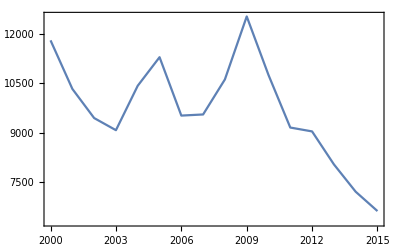

-Graphics-

```mathematica
DateListPlot[PridobiPodatke]
```

-Graphics-

```mathematica
Razlika2000= Normal[PridobiPodatke["2000"]- PridobiPodatke[leto]]
Razlika2015 = Normal[PridobiPodatke["2015"]- PridobiPodatke[leto]]
```

-723

-5892

```mathematica
StringForm["Med letoma 2000 in `` je bila razlika `` umrljih ljudi med letoma 2015 in `` pa ``.",leto, Razlika2000,leto,Razlika2015]
```

Med letoma 2000 in 2009 je bila razlika -723 umrljih ljudi med letoma 2015 in 2009 pa -5892.

## Aplikacija v oblaku

```mathematica
Prikazdrzave[drzava_]:= DateListPlot[Select[podatki, #["Country"]==Entity["Country",TextString[drzava]]&][[1]]["Aged1To59Months"],PlotLabel->StringForm["Graf umrljivosti za leta 2000-2015 za državo ``", TextString[drzava]],PlotTheme->"Scientific",ImageSize->Large]
```

```mathematica
aplikacija = FormPage["drzava"->"Country",Prikazdrzave[#drzava]&, AppearanceRules-><|"Title"->"Prikaz grafa poljubne države","Description" -> "Vnesi željeno državo za katero želiš videti graf","SubmitLabel"->"Prikazi"|> ]
```

```mathematica
CloudDeploy[aplikacija, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/c2caacbe-9577-4458-b94d-060627e46bcf]

## Prikazovanje trendov za eno državo iz zgornjih kontinentov

### Afrika

```mathematica
NigeriaPodatki = Select[podatki,#["Country"]==LinguisticAssistant&][[1]]["Aged0To4Years"];
PodatkiPoLetih1 =QuantityMagnitude[ Table[{x,NigeriaPodatki[TextString[x]]},{x,2000,2015}]];
premicaPovprecje1 = LinearModelFit[PodatkiPoLetih1,x,x];
```

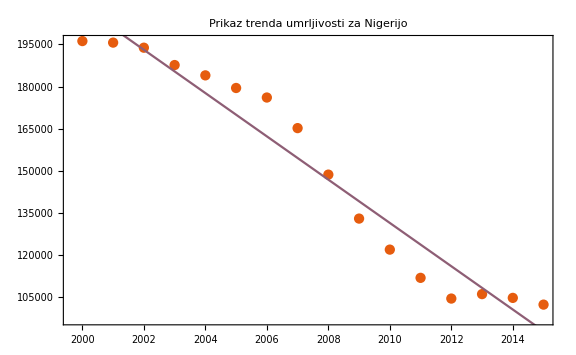

```mathematica
Show[ListPlot[PodatkiPoLetih1,ImageSize->Large,PlotTheme->"Scientific",PlotLabel->"Prikaz trenda umrljivosti za Nigerijo"],Plot[premicaPovprecje1["BestFit"],{x,2000,2015},ColorFunction->"Rainbow"]]
```

### Azija

```mathematica
IndonesiaPodatki = Select[podatki,#["Country"]==LinguisticAssistant&][[1]]["Aged0To4Years"];
PodatkiPoLetih2 =QuantityMagnitude[ Table[{x,IndonesiaPodatki[TextString[x]]},{x,2000,2015}]];
premicaPovprecje2 = LinearModelFit[PodatkiPoLetih2,x,x];
```

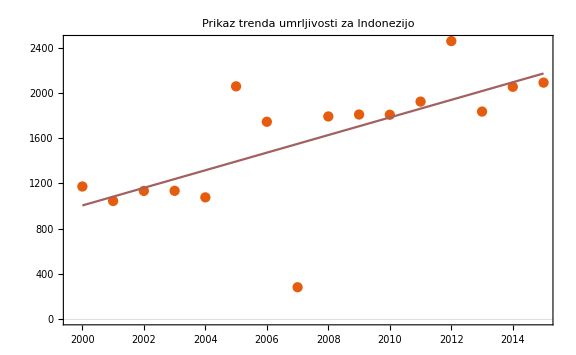

```mathematica
Show[ListPlot[PodatkiPoLetih2,ImageSize->Large,PlotTheme->"Scientific",PlotLabel->"Prikaz trenda umrljivosti za Indonezijo"],Plot[premicaPovprecje2["BestFit"],{x,2000,2015},ColorFunction->"Rainbow"]]
```

### Južna Amerika in Karibi

```mathematica
HaitiPodatki = Select[podatki,#["Country"]==LinguisticAssistant&][[1]]["Aged0To4Years"];
PodatkiPoLetih3 =QuantityMagnitude[ Table[{x,HaitiPodatki[TextString[x]]},{x,2000,2015}]];
premicaPovprecje3 = LinearModelFit[PodatkiPoLetih3,x,x];
```

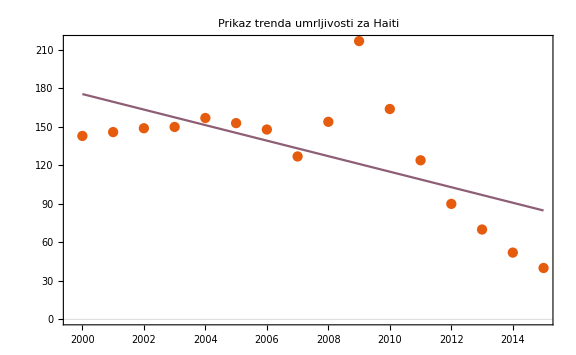

```mathematica
Show[ListPlot[PodatkiPoLetih3,ImageSize->Large,PlotTheme->"Scientific",PlotLabel->"Prikaz trenda umrljivosti za Haiti"],Plot[premicaPovprecje3["BestFit"],{x,2000,2015},ColorFunction->"Rainbow"]]
```